```mathematica
f[r_,mu_]:=1+r^2-(101 (2/7)^(1/3) r^(10/3))/(-2170 r^4-441 mu+3 Sqrt[7] Sqrt[532656 r^8+30380 r^4 mu+3087 mu^2])^(1/3)+(r^2 (-2170 r^4-441 mu+3 Sqrt[7] Sqrt[532656 r^8+30380 r^4 mu+3087 mu^2]))^(1/3)/(2^(1/3) 7^(2/3));
valorMu=4;
rh=r/. FindRoot[f[r,valorMu]==0,{r,0.8}]
```

0.825378

```mathematica
rc=r/. FindRoot[f[r,valorMu]==0,{r,0.2}]
```

0.178083

Power::infy: Infinite expression 1/0. encountered.

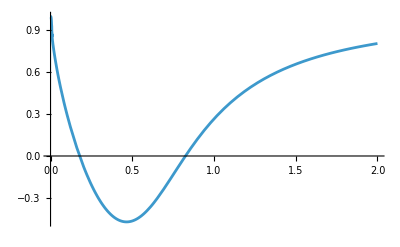

```mathematica
Plot[f[r,valorMu],{r,0,2}]
```

```mathematica
eps=10^-6
(*Región I:Exterior (r>rh)*)
rStarI=NDSolveValue[{y'[r]==1/f[r,valorMu],y[rh+eps]==0},y,{r,rh+eps,rh+5}];

(*Región II:Entre horizontes (rc<r<rh)*)
rStarII=NDSolveValue[{y'[r]==1/f[r,valorMu],y[(rc+rh)/2]==0},y,{r,rc+eps,rh-eps}];

(*Región III:Interior (0<r<rc)*)
rStarIII=NDSolveValue[{y'[r]==1/f[r,valorMu],y[rc-eps]==0},y,{r,eps,rc-eps}];
```

1/1000000

Power::infy: Infinite expression 1/0.^(1/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Union::normal: Nonatomic expression expected at position 1 in Automatic∪{{0.178083,r_c},{0.825378,r_h}}.

InterpolatingFunction::dmval: Input value {0.0000577184} lies outside the range of data in the interpolating function. Extrapolation will be used.

Union::normal: Nonatomic expression expected at position 1 in Automatic∪{{0.178083,r_c},{0.825378,r_h}}.

General::stop: Further output of Union::normal will be suppressed during this calculation.

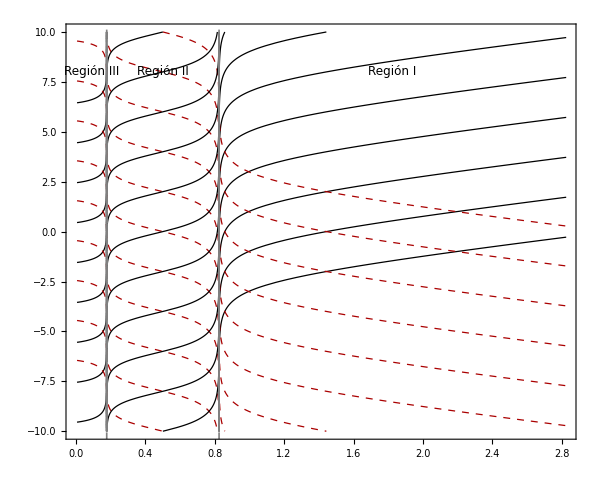

```mathematica
consts=Range[-10,10,2];
(*Configuración de estilo académico*)academicStyle={BaseStyle->{FontFamily->"Times",FontSize->14},Frame->True,FrameStyle->Black,GridLinesStyle->Directive[Gray,Dashed,Thickness[0.002]],ImageSize->600,AspectRatio->0.8};

(*Definición de las etiquetas de los horizontes para el eje r*)
tickLabels={{rc,"r_c"},{rh,"r_h"}};

Plot[{
Table[rStarI[r]+c,{c,consts}],Table[rStarII[r]+c,{c,consts}],Table[rStarIII[r]+c,{c,consts}],
Table[-rStarI[r]+c,{c,consts}],Table[-rStarII[r]+c,{c,consts}],Table[-rStarIII[r]+c,{c,consts}]
},{r,0,rh+2},PlotRange->{{0,rh+2},{-10,10}},Exclusions->{rc,rh},ExclusionsStyle->Directive[Gray,Dashed],PlotStyle->{Directive[Black,Thickness[0.0015]],(*Salientes*)Directive[Darker[Red],Thickness[0.0015],Dashed] },GridLines->{{rc,rh},None},FrameTicks->{{Automatic,None},{Union[Automatic/. FrameTicks->{Automatic,None},tickLabels],None}},(*Epilog para añadir etiquetas de texto directamente en el gráfico*)Epilog->{Text[Style["Región I",12,Italic],{rh+1,8}],Text[Style["Región II",12,Italic],{(rc+rh)/2,8}],Text[Style["Región III",12,Italic],{rc/2,8}]},Evaluate[academicStyle]
]
```